```mathematica
Quit
```

```mathematica
(* GA theory *)
```

```mathematica
poly[x_]:=x
polyxtox[x_]:=x^x
polyCPL[x_]:=x/(1+x)
polya[x_]:=(1/(1+x))^3
(* grammar={poly,Exp,Sin,Cos,Tan,Log};*)
grammar={poly};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammar]};
rang3={0,1};
rang4={0,9};
toursize=4;
selectionrate=0.3;
```

```mathematica
func[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]]x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomReal[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]
```

```mathematica
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomes=ParallelTable[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomReal[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[pigs=func[x,#,grammar]&/@chromosomes;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2marg[pigs[[j]],dataGA],.5],10^7],j},{j,1,Length[pigs]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigs[[fitness[[1,2]]]],chromosomes[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes[[p2[[jj,1]]]], chromosomes[[p2[[jj,2]]]]}],{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes[[p2[[jj,1]]]]],mutation[chromosomes[[p2[[jj,2]]]]]},{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function is: "];
Print[bestfitperstep[[-1,2]]];
Speak["The end"];];
bestfitperstep]
```

```mathematica
(* end *)
```

```mathematica
(* Cosmo Theory and Data *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
FileNames["..\\data\\mock_*Geff*"]
```

{..\data\mock_Eg_Geff.txt,..\data\mock_fs8_Geff.txt,..\data\mock_H_Geff.txt}

```mathematica
data=Import["..\\data\\mock_fs8_Geff.txt","Table"];
dataGA=data/.{z_,fs8_,sfs8_}->{(1/(1+z))^3,fs8/(1/(1+z)),sfs8/(1/(1+z))};
zmax=data[[All,1]]//Max;
```

```mathematica
(* Various params *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
Neff=3.046;
KtoeV=8.621738*10^-5;
```

```mathematica
(* Vanilla wCDM *)
dLwCDM[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
HwCDM[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
(* Growth for wCDM models *)
δwCDM[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δwCDM[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δwCDM[a,w,Ω]/δwCDM[1,w,Ω]
ΣwCDM[a_,w_,Ω_]:=2
ηwCDM[a_,w_,Ω_]:=1
EgwCDM[a_,w_,Ω_]:=(Ω ΣwCDM[a,w,Ω])/(2fwCDM[a,w,Ω])
P2wCDM[a_,w_,Ω_]:=2 EgwCDM[a,w,Ω]
P3wCDM[a_,w_,Ω_,σ8_]:=a D[Log[fσ8wCDM[aa,w,Ω,σ8]],aa]/.aa->a
```

```mathematica
(* DE equation of state w(a) and energy density f(a) *)
w[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
ρde[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
```

```mathematica
(* H(z) and χ^2 for the CPL model *) 
ρcr[h_]:=8.098*10^-11 h^2 eV^4;
Ωγ[h_]:=Pi^2/30 gγ T^4/ρcr[h]/.T->Tcmb K/.gγ->2/.GeV->10^9 eV/.K->KtoeV eV;
Ων[h_,Neff_]:=Neff*7/8(4/11)^(4/3)Ωγ[h]
aeq[om_?NumberQ,h_?NumberQ]:=(Ωγ[h]+Ων[h,Neff])/om;
H[a_,om_,w0_,wa_,n_,h_]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))ρde[a,w0,wa,n]]
(* The Geff and lensing potential. Not that in this notation: Geff=1 and Σ=2 in GR! *)
Geff[a_,ga_,m1_]:=1+ga (1-a)^m1-ga (1-a)^(2m1)
Σ[a_,σa_,m2_]:=2+σa (1-a)^m2-σa (1-a)^(2m2)
```

```mathematica
(* Solve the ODE for the growth *)
Clear[solgr,δ,fσ8,Eg]
aini=10^-4;
solgr[om_,w0_,wa_,n_,h_,ga_,m1_]:=solgr[om,w0,wa,n,h,ga,m1]=NDSolve[{δ''[a]+(3/a+(D[H[aa,om,w0,wa,n,h],aa]/.aa->a)/H[a,om,w0,wa,n,h])δ'[a]-3/2(om Geff[a,ga,m1])/(a^5(H[a,om,w0,wa,n,h]/H[1,om,w0,wa,n,h])^2)δ[a]==0,δ[aini]==aini,δ'[aini]==1},δ,{a,aini,1},Method->Automatic]
(* Define the growth-rate, fσ8 and Eg *)
f[a_,om_,w0_,wa_,n_,h_,ga_,m1_]:=a δ'[a]/δ[a]/.solgr[om,w0,wa,n,h,ga,m1][[1]]
fσ8[a_,om_,w0_,wa_,n_,h_,ga_,m1_,σ8_]:=σ8/δ[1] a δ'[a]/.solgr[om,w0,wa,n,h,ga,m1][[1]]
Eg[a_,om_,w0_,wa_,n_,h_,ga_,m1_,σ8_,σa_,m2_]:=(om Σ[a,σa,m2])/(2f[a,om,w0,wa,n,h,ga,m1])/.solgr[om,w0,wa,n,h,ga,m1][[1]]
```

```mathematica
chi2fs8[om_?NumericQ,w0_?NumericQ,wa_?NumericQ,n_?NumericQ,h_?NumericQ,ga_?NumericQ,m1_?NumericQ,σ8_?NumericQ]:=Sum[(1/data[[i,3]](data[[i,2]]-fσ8[1/(1+data[[i,1]]),om,w0,wa,n,h,ga,m1,σ8]))^2,{i,1,Length[data]}]
```

```mathematica
(* χ^2 for GA *)
chi2[f_,dat_]:=Module[{temp,ft},ft=(f/.x->#)&;temp=Sum[((dat[[ii,2]]-ft[dat[[ii,1]]])/dat[[ii,3]])^2,{ii,1,Length[dat]}];
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
chi2t[f_,dat_]:=Module[{temp,ft},ft=(f/.x->#)&;Sum[((dat[[ii,2]]-ft[dat[[ii,1]]])/dat[[ii,3]])^2,{ii,1,Length[dat]}]]
chi2marg[f_,dat_]:=Module[{temp,ft,A,B,Γ},ft=(f/.x->#)&;A=Sum[((dat[[ii,2]]-ft[dat[[ii,1]]])/dat[[ii,3]])^2,{ii,1,Length[dat]}];
B=Sum[((dat[[ii,2]]-ft[dat[[ii,1]]])/dat[[ii,3]]^2),{ii,1,Length[dat]}];
Γ=Sum[(1/dat[[ii,3]])^2,{ii,1,Length[dat]}];
temp=A-B^2/Γ;
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
offset[f_,dat_]:=Module[{ft,B,Γ},ft=(f/.x->#)&;B=Sum[((dat[[ii,2]]-ft[dat[[ii,1]]])/dat[[ii,3]]^2),{ii,1,Length[dat]}];
Γ=Sum[(1/dat[[ii,3]])^2,{ii,1,Length[dat]}];
B/Γ]
```

```mathematica
om0=0.3;
w00=-1;
wa0=0;
n0=1;
h0=0.7;
ga0=-0.627;
σa0=-3.562;
m10=2;
m20=2;
σ80=0.8;
(* Best fit // normal case *)
fmin=FindMinimum[chi2fs8[om,w00,wa0,n0,h0,ga,m10,σ8],{om,0.3,0.31},{ga,0.2,0.21},{σ8,0.8,0.81}]
Print["χ^2= ",fmin[[1]]]
Print["Number of points = ",Length[data]]
```

{16.0722,{om→0.294758,ga→-0.56333,σ8→0.794042}}

χ^2= 16.0722

Number of points = 20

```mathematica
chi2[fσ8[1/(1+x),om0,w00,wa0,n0,h0,ga0,m10,σ80],data]
chi2[fσ8[1/(1+x),0.3,w00,wa0,n0,h0,-0.56333,m10,0.7940],data]
```

20.3203

18.9336

```mathematica
(* end *)
```

```mathematica
(* GA fit *)
```

```mathematica
LaunchKernels[7];
```

```mathematica
generations=300;
Nseed=3;
Ncross=3;
Nmut=3;
prog`int=0;
prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,Nseed Ncross Nmut}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
Do[GApop[jj,kk,nn]=GAevo[1234jj,generations,100,0.65+0.05kk,0.20+0.05nn,False];prog`pop++;prog`int=0;,{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}];
```

```mathematica
ffname="Geff_mock_fs8_v2_sample_01";
Export[ffname<>".zip",{ffname<>".m"->Table[GApop[jj,kk,nn],{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}]}];
```

```mathematica
(* Use the following to read again the chains if necessary for further analysis *)
(*
ffname="Geff_mock_fs8_v2_sample_01";
GApop0=Import[ffname<>".zip",ffname<>".m"];
Do[GApop[i]=GApop0[[i]],{i,1,Length[GApop0]}];
*)
```

```mathematica
Rasterize[ListLogLogPlot[Partition[Flatten[Table[GApop[jj,kk,nn][[All,1]]//Abs,{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}]],generations],Joined->True,PlotRange->{5,10^5},Frame->True,FrameStyle->Black,Epilog->{Dashed,Line[{{0.1,fmin[[1]]},{generations,fmin[[1]]}}//Log]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,PlotLegends->Automatic],ImageSize->400,RasterSize->1000]
```

-Graphics-

```mathematica
fmin
```

{16.0722,{om→0.294758,ga→-0.56333,σ8→0.794042}}

```mathematica
chi2minGA=Partition[Flatten[Table[{jj,kk,nn,GApop[jj,kk,nn][[-1,1]]},{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}]],4];
SortBy[chi2minGA,Last]//Reverse
```

{{1,3,3,-16.5061},{1,2,2,-16.9543},{2,2,3,-17.5494},{1,2,3,-18.0972},{2,2,2,-18.6623},{1,3,2,-18.8237},{3,2,3,-19.1678},{1,2,1,-19.4655},{2,3,3,-20.1466},{1,3,1,-20.7677},{2,3,2,-20.9662},{2,1,2,-21.0558},{2,1,3,-21.5336},{1,1,1,-21.723},{1,1,2,-23.7225},{3,1,2,-23.9606},{2,2,1,-24.3274},{2,3,1,-24.3403},{2,1,1,-24.3447},{3,3,3,-27.0157},{3,1,3,-29.0783},{3,2,1,-33.3544},{3,3,2,-35.6523},{3,2,2,-39.3019},{3,3,1,-46.8115},{1,1,3,-51.8049},{3,1,1,-64.367}}

```mathematica
GApop[1,3,3][[-1,2]]
%/.x->X
%/.X->a^3//PowerExpand
```

-0.865228 x^0.427231+0.106566 x^1.87773-0.0149742 x^8.10963

-0.865228 X^0.427231+0.106566 X^1.87773-0.0149742 X^8.10963

-0.865228 a^1.28169+0.106566 a^5.63318-0.0149742 a^24.3289

```mathematica
Clear[fσ8GA0,off,fσ8GA]
fσ8GA0[X_]:=-0.8652275944329362 X^0.42723143508048267+0.10656616386919483 X^1.877727974263708-0.014974203366821854 X^8.109630440536886;
off=offset[fσ8GA0[x],dataGA]
fσ8GA[a_]:=a(off+fσ8GA0[X]/.X->a^3)
```

1.1547

```mathematica
(* Ωm & σ8 in ΛCDM from growth *)
Ωm->1/NIntegrate[3 fσ8wCDM[x,-1,0.3,0.8]/fσ8wCDM[1,-1,0.3,0.8] NIntegrate[fσ8wCDM[y,-1,0.3,0.8]/(y fσ8wCDM[1,-1,0.3,0.8]),{y,0,x}],{x,0,1}]//Quiet
σ8->NIntegrate[fσ8wCDM[a,-1,0.3,0.8]/a,{a,0,1}]
```

Ωm→0.3

σ8→0.8

```mathematica
(* Ωm in GA from growth *)
Ωm->1/NIntegrate[3 fσ8GA[a1]/fσ8GA[1] NIntegrate[fσ8GA[y]/(y fσ8GA[1]),{y,0,a1}],{a1,0,1}]//Quiet
σ8->NIntegrate[fσ8GA[xx]/xx,{xx,0,1}]
```

Ωm→0.271304

σ8→0.790971

```mathematica
chi2[fσ8[1/(1+x),fmin[[2,1,2]],w00,wa0,n0,h0,fmin[[2,2,2]],m10,fmin[[2,3,2]]],data]
chi2[fσ8GA[1/(1+x)],data]
```

16.0722

16.5061

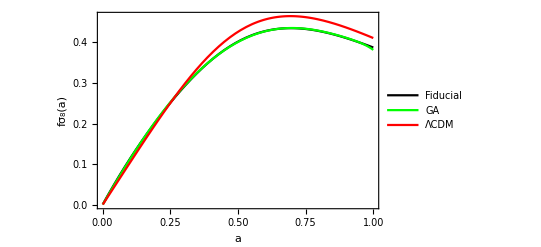

```mathematica
Plot[{fσ8[a,fmin[[2,1,2]],w00,wa0,n0,h0,fmin[[2,2,2]],m10,fmin[[2,3,2]]],fσ8GA[a],fσ8wCDM[a,-1,0.3,0.8]},{a,10^-3,1},PlotStyle->{Black,Green,Red},PlotLegends->{"Fiducial","GA","ΛCDM"},Frame->True,FrameStyle->Black,FrameLabel->{"a","fσ_8(a)"}]
```

```mathematica
dfs8[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 data[[i,3]])(dfs8[data[[i,1]],a1,a2,a3,a4]+fσ8GA[1/(1+data[[i,1]])]-data[[i,2]])]+Erf[1/(√2 data[[i,3]])(dfs8[data[[i,1]],a1,a2,a3,a4]-fσ8GA[1/(1+data[[i,1]])]+data[[i,2]])]),{i,1,Length[data]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[data]}]]
```

```mathematica
chi2ga[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=chi2[fσ8GA[1/(1+x)]+dfs8[x,a1,a2,a3,a4],data]
```

```mathematica
chi2tot[a1_,a2_,a3_,a4_]:=chi2CI[a1,a2,a3,a4]+chi2ga[a1,a2,a3,a4]
```

```mathematica
fminerr1=FindMinimum[chi2tot[a1,0,0,0],{a1,0.11,0.111},MaxIterations->500]
fminerr2=FindMinimum[chi2tot[a1,a2,0,0],{a1,0.11,0.111},{a2,0.11,0.111},MaxIterations->500]
fminerr3=FindMinimum[chi2tot[a1,a2,a3,0],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},MaxIterations->500]
fminerr4=FindMinimum[chi2tot[a1,a2,a3,a4],{a1,0.11,0.111},{a2,0.11,0.111},{a3,0.11,0.111},{a4,0.11,0.111},MaxIterations->500]
```

{23.7079,{a1→0.00105907}}

{23.522,{a1→0.00164266,a2→-0.000534973}}

{22.8056,{a1→0.00017835,a2→0.00367091,a3→-0.00203474}}

{21.5798,{a1→0.0020563,a2→-0.00632123,a3→0.00720296,a4→-0.00131459}}

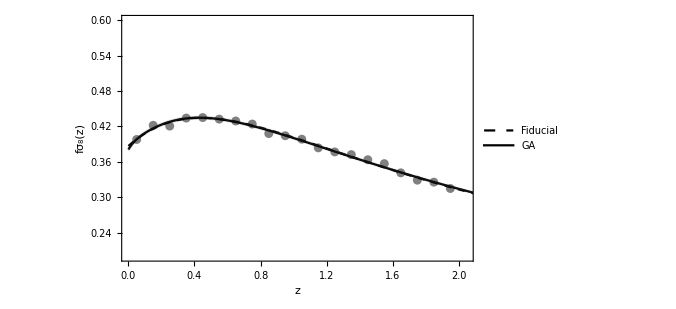

```mathematica
ϵ0={-1,0,1};
col=GrayLevel[0.3,0.2];
plr={{0,1.05zmax},{0.2,0.6}};
pldata=Show[ErrorListPlot[data,PlotRange->plr,PlotStyle->Gray],Plot[{fσ8[1/(1+x),fmin[[2,1,2]],w00,wa0,n0,h0,fmin[[2,2,2]],m10,fmin[[2,3,2]]],fσ8GA[1/(1+x)]+ dfs8[x,a1,a2,0,0]ϵ0/.fminerr2[[2]]}//Evaluate,{x,0,2 zmax},PlotStyle->{{Dashed,Black},col,Black,col},Filling->{2->{{4},col}},PlotRange->plr,Frame->True,PlotLegends->Placed[LineLegend[{{Dashed,Black},Black},{"Fiducial","GA"}],Scaled[{0.85,0.85}]]],Frame->True,Axes->False,FrameLabel->{"z","fσ_8(z)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr,ImageSize->500]
```

```mathematica
datares=Table[{data[[i,1]],data[[i,2]]-fσ8[1/(1+data[[i,1]]),fmin[[2,1,2]],w00,wa0,n0,h0,fmin[[2,2,2]],m10,fmin[[2,3,2]]],data[[i,3]]},{i,1,Length[data]}];
```

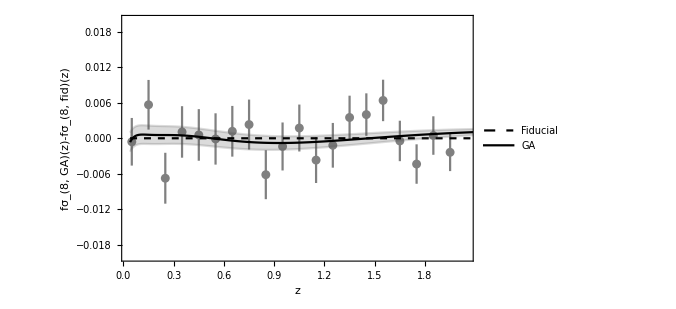

```mathematica
col=GrayLevel[0.3,0.2];
plr={{0.03,1.05 zmax},{-1,1}/50};
plHzdatares=Show[ErrorListPlot[datares,PlotRange->plr,PlotStyle->Gray],Plot[{0,fσ8GA[1/(1+x)]+( dfs8[x,a1,a2,0,0]ϵ0/.fminerr2[[2]])-(fσ8[1/(1+x),fmin[[2,1,2]],w00,wa0,n0,h0,fmin[[2,2,2]],m10,fmin[[2,3,2]]])}//Evaluate,{x,0.04,2 zmax},PlotStyle->{{Dashed,Black},col,Black,col},Filling->{2->{{4},col}},PlotRange->plr,Frame->True,PlotLegends->Placed[LineLegend[{{Dashed,Black},Black},{"Fiducial","GA"}],Scaled[{0.87,0.87}]]],Frame->True,Axes->False,FrameLabel->{"z","fσ_(8, GA)(z)-fσ_(8, fid)(z)"},FrameStyle->Black,BaseStyle->FontSize->15,PlotRange->plr,ImageSize->500]
```

```mathematica
(* end *)
```